# Submissions to the WTC 2020 One-Liner Competition

Variable names used in some submissions may clash.  If an entry doesn’t not appear to work, try quitting the kernel to clear all variable definitions and evaluating again.

## Chessboard in a Tweet (128 characters)

## Author : Mike Sollami

```mathematica
Graphics@{Raster@Array[.9^+##&,{8,8}],MapIndexed[Locator[#2-.5,#]&,{b={♖,♘,♗,♕,♔,♗,♘,♖},y=Table[♙,8],3, , , ,y,b},{2}]/. 3->Red}
```

-Graphics-

## Audial Mirror (128 characters)

## Author : Mike Sollami

```mathematica
ResourceFunction["ToggleButton"]@{"record":>(s=AudioRecord[]),"reflect":>(AudioStop[];AudioPlay@AudioReverse@AudioTrim@Audio@s)}
```

## Mars (125 characters)

## Author: Jack Madden

```mathematica
m=TravelDirections[{Here,LinguisticAssistant}];
If[FailureQ[m],"No flights to Mars yet", Print["Wow ok, have a nice trip!"];m["Dataset"]]
```

No flights to Mars yet

## Wolf (127 characters)

## Author: Jack Madden

```mathematica
Colorize[Rasterize[$UserName Style[🐺,FontSize->99]],ColorFunction->RandomChoice[ColorData["Gradients"]]]
BlockchainPut[%]
```

-Graphics-

522cff55960d0544d8af6e41685c004472188c41a6b49495fb0fed78252d403a

## Bach raised to the N-th Power (127 characters)

## Author: James Lu

Bach is a master of counterpoint, with his music containing melodic lines that are harmonically interdependent on each other. Here, with the help of Wolfram Language we’ve raised Bach’s counterpoint to the N-th power, by successively adding layers on top of the original to provide an added dimension of harmonic complexity. Would Bach have done this to explore harmonies if he had access to Wolfram Language? One will have to listen to the music and make your own judgement.

```mathematica
AudioChannelCombine@MapIndexed[AudioAmplify[#1,2/#2[[1]]]~AudioPad~{6#2[[1]]-6,0}&,Import["https://wolfr.am/Zds5yDLH"]~Table~3]
```

## Geo QUIZ - Capital Cities (128 characters)

## Author: Catalin Popescu

{United States Virgin Islands,Guyana,Iraq,Djibouti,Paraguay,Wallis and Futuna Islands}

CapitalCity

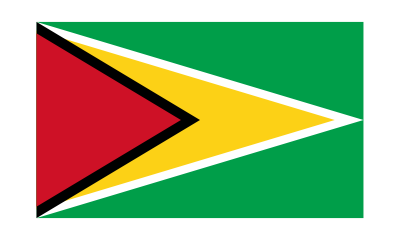
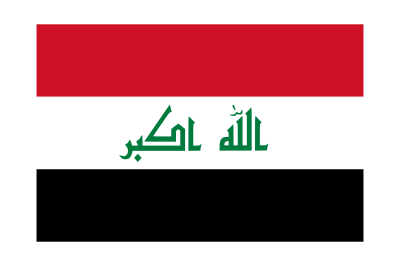
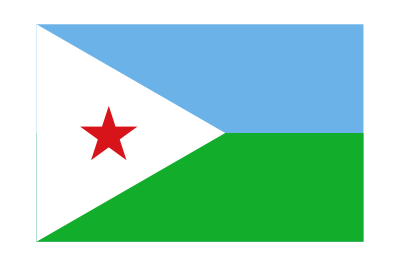
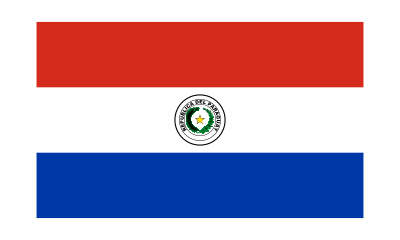

{-Graphics- United States Virgin Islands,-Graphics- Guyana,-Graphics- Iraq,-Graphics- Djibouti,-Graphics- Paraguay,-Graphics- Wallis and Futuna Islands}

```mathematica
RandomEntity["Country",6]
"CapitalCity"
Panel[#["Flag"],Tooltip[#["Name"],#[%]]SetterBar[0,Sort@GeoNearest["City",#[%],3]]]&/@%%
```

## Minute Repeater Computa UltraTerse (122 characters)

## Author: James Lu

“Minute Repeater” is a complication of mechanical watches and one of the most fascinating accomplishments of of Haute Horlogerie. At the press of a button, a minute repeater watch would chime out the hour, followed by the quarter hour and minutes. For example, if the time is 3:34am then the minute repeater will sound 3 low tones representing 3 hours, 2 sequence of dual-tones representing 2×15=30 minutes, and 4 high tones representing 4 minutes: “ding, ding, ding; ding+dong, ding+dong; ding, ding, ding, ding”. Such watches originated before night illumination became widely available and it was invaluable for the visually impaired. In the current day, while minute repeater watches have lost their practical utility, they are still highly sought after by watch enthusiasts due to their intricacy and novelty. 

The mechanisms underlying minute repeater watches are ingenious and require both technical facility as well as musicality on the part of the watchmaker to listen to and confirm the harmony of the striking sounds.  Furthermore, the pinnacle of achievement for minute repeater movements is their ability to fit into a small watch case. As a tribute to this mechanism, I’ve utilized the computational “gears” of Wolfram Language and implemented a terse code succinct enough to fit into a 128 character “case”. At the press of “evaluate”, this minute repeater watch tells time in a manner that harkens back to an earlier age but relies on modern computation.

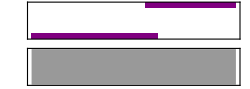

```mathematica
Sound@Flatten@MapThread[#1~Table~#2&,{SoundNote[#,0.7]&/@{0,{0,7},7},{#[[4]],Floor[#[[5]]/15],#[[5]]~Mod~15}&@DateList[]}]
```

## Poor Man’s Vacation (126 characters)

## Author : Mike Sollami

```mathematica
d=Dynamic
d@x~LocatorPane~GeoGraphics[c=CityData[]~Take~-20]
n=Nearest[Reverse@@#@"Position"->WebImageSearch@#[[2]]&/@c]
d@n@x
```

Dynamic

NearestFunction[{2, <>}]

## Untitled QR code (127 characters)

## Author : Roel Fledderman

```mathematica
AnimatedImage@Table[ImageResize[ImageTrim[BarcodeImage[ToString@RandomReal[1,9],"QR"],{j=130,j},r,Padding->1],j],{r,450,1,-15}]
```

## Exoplanet (128 characters)

## Author: Jack Madden

```mathematica
"The planet, "<>Sort[ExoplanetData[All,{"Altitude","Name"}]][[-1,2]]<>", is right above you. Could they be thinking of you too?"
```

Quantity::unkunit: Unable to interpret unit specification MixedUnit[{AngularDegrees,Arcminutes,Arcseconds}].

General::stop: Further output of Quantity::unkunit will be suppressed during this calculation.

The planet, Kepler 923 b, is right above you. Could they be thinking of you too?

## Bifurcation diagram (126 characters)

## Author: Benny Chang

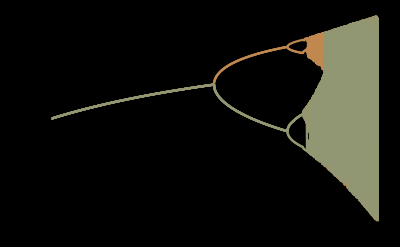

```mathematica
Plot[FixedPoint[x#(1-#)&,Range[10]/15.,1000],{x,2,4},ColorFunction->Function[{x,y},ColorData["Rainbow"][y]],Background->Black]
```